```mathematica
ClearAll["Global`*"]
```

```mathematica
Remove[starvation,M,B0,Bm,η,γ,f0,Em]
starvation =  ts*-Bm/(Em*Log[1-f0*M^(γ-1)]);
recovery = ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]);
Ratio = FullSimplify[starvation/recovery]
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
(*rhovalues = Table[x,{x,0.2,0.7,0.1}];*)
(*scalevalues = Table[x,{x,6,0.5,-0.6}];*)
(*sigmavalues =Table[x,{x,starvation/200,starvation/0.4,0.0000005}];*)
sigmavalues = RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==2.3060191710825582*^-7},B,{n,1,336}];
ExtinctionSigma = ParallelTable[
Reps = 1000;
ProportionExtinct=With[{
α=resourcegrowth,λ=growth,σ=sigma,ρ=recovery,β=maintenance,μ=mortality,T=100000000,thresholdpercent=0.5,PercentPerturbed=1},
ExtinctionReps = Table[
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*Set threshold as percent of equilibrial state*)
threshold =4.016366413626103;(* ((α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)))*thresholdpercent;*)
(*F0=RandomReal[{1000,30000}];
H0 = RandomReal[{1000,30000}];
R0 = RandomReal[{1000,30000}];*)
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;1000,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma/ρ,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigmavalues}(*,{rho,rhovalues}*)];
```

NDSolve::ndsz: At t == 1.91363×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 1.22668×10^7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 392920., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {12300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 423637., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 1.02558×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 1.37196×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.52352×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.11861×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.7489×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.87094×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 839391., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.15469×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 209042., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 161232., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 208304., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat",ExtinctionSigma]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat

```mathematica
ExtinctionSigma=ToExpression[Import["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat","Data"]];
```

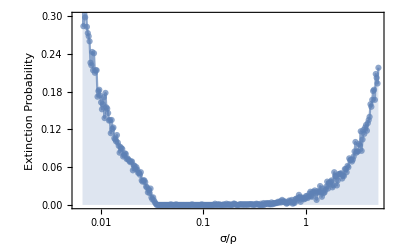

```mathematica
ExtinctionsAllometricPlot=Show[{
ListLogLinearPlot[ExtinctionSigma,PlotRange->{{0.006,5},{0,0.3}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListLogLinearPlot[ExtinctionSigma,PlotRange->{0,0.5},Joined->True,Filling->Bottom,PlotStyle->Directive[Opacity[0.7]]](*,
step=10;If[EvenQ[step],step=step+1];
ListLogLinearPlot[
MovingAverage[
Re[ExtinctionSigma],step],PlotStyle->ColorData[97,8],Joined->True(*Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True*)
]*)
},ImageSize->400]
```

```mathematica
Ratio
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
RatioValues=(
noise=0.5;
ParallelTable[
value=Re[Ratio/.{
M->10^2,
η->3/4,
γ->1.19,
f0->0.0202*(1+RandomReal[{-noise,noise}]),
B0->1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
Bm->0.0245*(1+RandomReal[{-noise,noise}])
}];
{value,i},
{i,0.1,10,0.001}]
);
```

```mathematica
RatioValuePlot=ListLogLinearPlot[RatioValues,PlotRange->{{0.006,5},All},FrameTicks->None,Frame->True,AspectRatio->1/10,PlotStyle->Directive[{Opacity[0.05]}]]
```

-Graphics-

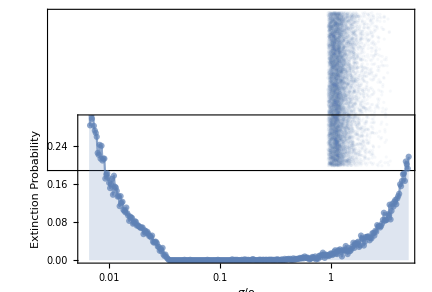

```mathematica
CombinedAllometricPlot=GraphicsColumn[{
Show[RatioValuePlot,ImagePadding->{{43,14},{Automatic,Automatic}}],
Show[
ExtinctionsAllometricPlot,ImagePadding->{{40,10},{Automatic,Automatic}}]},Spacings->Scaled[-0.65],ImagePadding->{{0,0},{110,40}}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",CombinedAllometricPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf

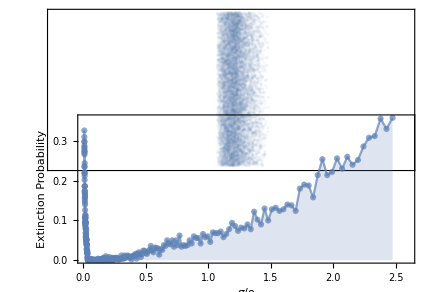

```mathematica
ExtinctionsAllometricPlot2=Show[{
ListPlot[ExtinctionSigma,PlotRange->{{0.006,2.6},{0,All}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True,Filling->Bottom,PlotStyle->Directive[Opacity[0.7]]](*,
step=10;If[EvenQ[step],step=step+1];
ListLogLinearPlot[
MovingAverage[
Re[ExtinctionSigma],step],PlotStyle->ColorData[97,8],Joined->True(*Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True*)
]*)
},ImageSize->400];
RatioValuePlot2=ListPlot[RatioValues,PlotRange->{{0.006,2.6},All},FrameTicks->None,Frame->True,AspectRatio->1/10,PlotStyle->Directive[{Opacity[0.05]}]];
CombinedAllometricPlot=GraphicsColumn[{
Show[RatioValuePlot2,ImagePadding->{{43,14},{Automatic,Automatic}}],
Show[
ExtinctionsAllometricPlot2,ImagePadding->{{40,10},{Automatic,Automatic}}]},Spacings->Scaled[-0.65],ImagePadding->{{0,0},{110,40}}]
```

```mathematica
With[{
α=resourcegrowth,λ=growth,σ=sigma,ρ=recovery,β=maintenance,μ=mortality,T=100000000,thresholdpercent=0.2,PercentPerturbed=1},
Table[
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*Set threshold as percent of equilibrial state*)
threshold = Re[((α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)))]*0.5,
{sigma,sigmavalues}]
]
```

{391.903,390.411,388.9,387.372,385.825,384.26,382.676,381.075,379.455,377.817,376.16,374.485,372.793,371.081,369.352,367.605,365.84,364.057,362.256,360.437,358.6,356.746,354.875,352.986,351.08,349.157,347.218,345.261,343.288,341.299,339.293,337.271,335.234,333.181,331.113,329.03,326.932,324.819,322.692,320.551,318.396,316.228,314.046,311.852,309.645,307.426,305.196,302.953,300.7,298.436,296.161,293.876,291.582,289.278,286.966,284.645,282.316,279.979,277.635,275.284,272.927,270.564,268.196,265.822,263.444,261.062,258.676,256.287,253.895,251.501,249.106,246.708,244.31,241.912,239.513,237.115,234.718,232.323,229.929,227.538,225.15,222.765,220.384,218.007,215.635,213.268,210.907,208.552,206.203,203.861,201.526,199.199,196.881,194.571,192.27,189.978,187.696,185.424,183.163,180.912,178.673,176.446,174.23,172.027,169.836,167.659,165.494,163.343,161.206,159.083,156.974,154.88,152.801,150.737,148.689,146.656,144.639,142.638,140.653,138.684,136.732,134.797,132.879,130.978,129.094,127.227,125.378,123.547,121.733,119.937,118.159,116.399,114.656,112.932,111.226,109.538,107.869,106.217,104.584,102.97,101.373,99.7947,98.2346,96.6929,95.1694,93.6641,92.1769,90.7079,89.257,87.8241,86.4092,85.0122,83.633,82.2716,80.9279,79.6018,78.2932,77.002,75.7282,74.4715,73.232,72.0095,70.8039,69.6151,68.4429,67.2873,66.1481,65.0251,63.9183,62.8275,61.7526,60.6935,59.6499,58.6219,57.6091,56.6115,55.6289,54.6612,53.7082,52.7698,51.8458,50.9361,50.0405,49.1589,48.2911,47.4369,46.5962,45.7689,44.9547,44.1536,43.3653,42.5898,41.8268,41.0762,40.3378,39.6116,38.8972,38.1946,37.5037,36.8242,36.1561,35.4991,34.8531,34.218,33.5935,32.9797,32.3762,31.783,31.2,30.6269,30.0636,29.51,28.966,28.4314,27.906,27.3898,26.8825,26.3841,25.8944,25.4133,24.9407,24.4763,24.0202,23.5721,23.132,22.6997,22.2751,21.858,21.4484,21.0461,20.651,20.263,19.882,19.5079,19.1405,18.7797,18.4255,18.0777,17.7362,17.4009,17.0718,16.7486,16.4313,16.1199,15.8141,15.5139,15.2193,14.9301,14.6462,14.3675,14.094,13.8255,13.562,13.3034,13.0496,12.8005,12.556,12.3161,12.0806,11.8495,11.6227,11.4002,11.1818,10.9675,10.7573,10.5509,10.3485,10.1498,9.95488,9.76362,9.57596,9.39184,9.21118,9.03394,8.86004,8.68943,8.52205,8.35783,8.19673,8.03867,7.88362,7.7315,7.58228,7.43589,7.29228,7.1514,7.01321,6.87765,6.74467,6.61423,6.48627,6.36076,6.23764,6.11688,5.99843,5.88224,5.76828,5.65649,5.54685,5.43931,5.33383,5.23037,5.1289,5.02938,4.93177,4.83603,4.74214,4.65005,4.55973,4.47115,4.38427,4.29907,4.2155,4.13355,4.05318,3.97436,3.89706,3.82125,3.7469,3.67399,3.60249,3.53236,3.4636,3.39616,3.33003,3.26517,3.20157,3.1392,3.07804,3.01806,2.95925,2.90157,2.84501,2.78955,2.73516,2.68182}

```mathematica
With[{
α=resourcegrowth,λ=growth,σ=starvation,ρ=recovery,β=maintenance,μ=mortality,T=100000000,thresholdpercent=0.2,PercentPerturbed=1},
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*Set threshold as percent of equilibrial state*)
threshold = Re[((α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)))]*0.2
]
```

4.01637

```mathematica
sigmavalues = RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==2.3060191710825582*^-7},B,{n,1,336}]/recovery
```

{0.00663806+0. ⅈ,0.00677082+0. ⅈ,0.00690624+0. ⅈ,0.00704436+0. ⅈ,0.00718525+0. ⅈ,0.00732895+0. ⅈ,0.00747553+0. ⅈ,0.00762504+0. ⅈ,0.00777754+0. ⅈ,0.0079331+0. ⅈ,0.00809176+0. ⅈ,0.00825359+0. ⅈ,0.00841866+0. ⅈ,0.00858704+0. ⅈ,0.00875878+0. ⅈ,0.00893395+0. ⅈ,0.00911263+0. ⅈ,0.00929489+0. ⅈ,0.00948078+0. ⅈ,0.0096704+0. ⅈ,0.00986381+0. ⅈ,0.0100611+0. ⅈ,0.0102623+0. ⅈ,0.0104676+0. ⅈ,0.0106769+0. ⅈ,0.0108904+0. ⅈ,0.0111082+0. ⅈ,0.0113304+0. ⅈ,0.011557+0. ⅈ,0.0117882+0. ⅈ,0.0120239+0. ⅈ,0.0122644+0. ⅈ,0.0125097+0. ⅈ,0.0127599+0. ⅈ,0.0130151+0. ⅈ,0.0132754+0. ⅈ,0.0135409+0. ⅈ,0.0138117+0. ⅈ,0.0140879+0. ⅈ,0.0143697+0. ⅈ,0.0146571+0. ⅈ,0.0149502+0. ⅈ,0.0152492+0. ⅈ,0.0155542+0. ⅈ,0.0158653+0. ⅈ,0.0161826+0. ⅈ,0.0165063+0. ⅈ,0.0168364+0. ⅈ,0.0171731+0. ⅈ,0.0175166+0. ⅈ,0.0178669+0. ⅈ,0.0182243+0. ⅈ,0.0185887+0. ⅈ,0.0189605+0. ⅈ,0.0193397+0. ⅈ,0.0197265+0. ⅈ,0.0201211+0. ⅈ,0.0205235+0. ⅈ,0.0209339+0. ⅈ,0.0213526+0. ⅈ,0.0217797+0. ⅈ,0.0222153+0. ⅈ,0.0226596+0. ⅈ,0.0231128+0. ⅈ,0.023575+0. ⅈ,0.0240465+0. ⅈ,0.0245275+0. ⅈ,0.025018+0. ⅈ,0.0255184+0. ⅈ,0.0260287+0. ⅈ,0.0265493+0. ⅈ,0.0270803+0. ⅈ,0.0276219+0. ⅈ,0.0281743+0. ⅈ,0.0287378+0. ⅈ,0.0293126+0. ⅈ,0.0298988+0. ⅈ,0.0304968+0. ⅈ,0.0311067+0. ⅈ,0.0317289+0. ⅈ,0.0323635+0. ⅈ,0.0330107+0. ⅈ,0.0336709+0. ⅈ,0.0343444+0. ⅈ,0.0350312+0. ⅈ,0.0357319+0. ⅈ,0.0364465+0. ⅈ,0.0371754+0. ⅈ,0.0379189+0. ⅈ,0.0386773+0. ⅈ,0.0394509+0. ⅈ,0.0402399+0. ⅈ,0.0410447+0. ⅈ,0.0418656+0. ⅈ,0.0427029+0. ⅈ,0.043557+0. ⅈ,0.0444281+0. ⅈ,0.0453167+0. ⅈ,0.046223+0. ⅈ,0.0471474+0. ⅈ,0.0480904+0. ⅈ,0.0490522+0. ⅈ,0.0500332+0. ⅈ,0.0510339+0. ⅈ,0.0520546+0. ⅈ,0.0530957+0. ⅈ,0.0541576+0. ⅈ,0.0552407+0. ⅈ,0.0563456+0. ⅈ,0.0574725+0. ⅈ,0.0586219+0. ⅈ,0.0597944+0. ⅈ,0.0609902+0. ⅈ,0.0622101+0. ⅈ,0.0634543+0. ⅈ,0.0647233+0. ⅈ,0.0660178+0. ⅈ,0.0673382+0. ⅈ,0.0686849+0. ⅈ,0.0700586+0. ⅈ,0.0714598+0. ⅈ,0.072889+0. ⅈ,0.0743468+0. ⅈ,0.0758337+0. ⅈ,0.0773504+0. ⅈ,0.0788974+0. ⅈ,0.0804753+0. ⅈ,0.0820848+0. ⅈ,0.0837265+0. ⅈ,0.0854011+0. ⅈ,0.0871091+0. ⅈ,0.0888513+0. ⅈ,0.0906283+0. ⅈ,0.0924409+0. ⅈ,0.0942897+0. ⅈ,0.0961755+0. ⅈ,0.098099+0. ⅈ,0.100061+0. ⅈ,0.102062+0. ⅈ,0.104103+0. ⅈ,0.106185+0. ⅈ,0.108309+0. ⅈ,0.110475+0. ⅈ,0.112685+0. ⅈ,0.114939+0. ⅈ,0.117237+0. ⅈ,0.119582+0. ⅈ,0.121974+0. ⅈ,0.124413+0. ⅈ,0.126901+0. ⅈ,0.12944+0. ⅈ,0.132028+0. ⅈ,0.134669+0. ⅈ,0.137362+0. ⅈ,0.14011+0. ⅈ,0.142912+0. ⅈ,0.14577+0. ⅈ,0.148685+0. ⅈ,0.151659+0. ⅈ,0.154692+0. ⅈ,0.157786+0. ⅈ,0.160942+0. ⅈ,0.164161+0. ⅈ,0.167444+0. ⅈ,0.170793+0. ⅈ,0.174209+0. ⅈ,0.177693+0. ⅈ,0.181247+0. ⅈ,0.184872+0. ⅈ,0.188569+0. ⅈ,0.19234+0. ⅈ,0.196187+0. ⅈ,0.200111+0. ⅈ,0.204113+0. ⅈ,0.208195+0. ⅈ,0.212359+0. ⅈ,0.216606+0. ⅈ,0.220939+0. ⅈ,0.225357+0. ⅈ,0.229864+0. ⅈ,0.234462+0. ⅈ,0.239151+0. ⅈ,0.243934+0. ⅈ,0.248813+0. ⅈ,0.253789+0. ⅈ,0.258865+0. ⅈ,0.264042+0. ⅈ,0.269323+0. ⅈ,0.274709+0. ⅈ,0.280204+0. ⅈ,0.285808+0. ⅈ,0.291524+0. ⅈ,0.297354+0. ⅈ,0.303301+0. ⅈ,0.309367+0. ⅈ,0.315555+0. ⅈ,0.321866+0. ⅈ,0.328303+0. ⅈ,0.334869+0. ⅈ,0.341567+0. ⅈ,0.348398+0. ⅈ,0.355366+0. ⅈ,0.362473+0. ⅈ,0.369723+0. ⅈ,0.377117+0. ⅈ,0.384659+0. ⅈ,0.392353+0. ⅈ,0.4002+0. ⅈ,0.408204+0. ⅈ,0.416368+0. ⅈ,0.424695+0. ⅈ,0.433189+0. ⅈ,0.441853+0. ⅈ,0.45069+0. ⅈ,0.459704+0. ⅈ,0.468898+0. ⅈ,0.478276+0. ⅈ,0.487841+0. ⅈ,0.497598+0. ⅈ,0.50755+0. ⅈ,0.517701+0. ⅈ,0.528055+0. ⅈ,0.538616+0. ⅈ,0.549388+0. ⅈ,0.560376+0. ⅈ,0.571584+0. ⅈ,0.583015+0. ⅈ,0.594676+0. ⅈ,0.606569+0. ⅈ,0.618701+0. ⅈ,0.631075+0. ⅈ,0.643696+0. ⅈ,0.65657+0. ⅈ,0.669701+0. ⅈ,0.683095+0. ⅈ,0.696757+0. ⅈ,0.710692+0. ⅈ,0.724906+0. ⅈ,0.739404+0. ⅈ,0.754192+0. ⅈ,0.769276+0. ⅈ,0.784662+0. ⅈ,0.800355+0. ⅈ,0.816362+0. ⅈ,0.832689+0. ⅈ,0.849343+0. ⅈ,0.86633+0. ⅈ,0.883657+0. ⅈ,0.90133+0. ⅈ,0.919356+0. ⅈ,0.937744+0. ⅈ,0.956498+0. ⅈ,0.975628+0. ⅈ,0.995141+0. ⅈ,1.01504+0. ⅈ,1.03534+0. ⅈ,1.05605+0. ⅈ,1.07717+0. ⅈ,1.09872+0. ⅈ,1.12069+0. ⅈ,1.1431+0. ⅈ,1.16597+0. ⅈ,1.18929+0. ⅈ,1.21307+0. ⅈ,1.23733+0. ⅈ,1.26208+0. ⅈ,1.28732+0. ⅈ,1.31307+0. ⅈ,1.33933+0. ⅈ,1.36612+0. ⅈ,1.39344+0. ⅈ,1.42131+0. ⅈ,1.44973+0. ⅈ,1.47873+0. ⅈ,1.5083+0. ⅈ,1.53847+0. ⅈ,1.56924+0. ⅈ,1.60062+0. ⅈ,1.63263+0. ⅈ,1.66529+0. ⅈ,1.69859+0. ⅈ,1.73256+0. ⅈ,1.76722+0. ⅈ,1.80256+0. ⅈ,1.83861+0. ⅈ,1.87538+0. ⅈ,1.91289+0. ⅈ,1.95115+0. ⅈ,1.99017+0. ⅈ,2.02998+0. ⅈ,2.07057+0. ⅈ,2.11199+0. ⅈ,2.15423+0. ⅈ,2.19731+0. ⅈ,2.24126+0. ⅈ,2.28608+0. ⅈ,2.3318+0. ⅈ,2.37844+0. ⅈ,2.42601+0. ⅈ,2.47453+0. ⅈ,2.52402+0. ⅈ,2.5745+0. ⅈ,2.62599+0. ⅈ,2.67851+0. ⅈ,2.73208+0. ⅈ,2.78672+0. ⅈ,2.84246+0. ⅈ,2.8993+0. ⅈ,2.95729+0. ⅈ,3.01644+0. ⅈ,3.07677+0. ⅈ,3.1383+0. ⅈ,3.20107+0. ⅈ,3.26509+0. ⅈ,3.33039+0. ⅈ,3.397+0. ⅈ,3.46494+0. ⅈ,3.53424+0. ⅈ,3.60492+0. ⅈ,3.67702+0. ⅈ,3.75056+0. ⅈ,3.82557+0. ⅈ,3.90208+0. ⅈ,3.98012+0. ⅈ,4.05973+0. ⅈ,4.14092+0. ⅈ,4.22374+0. ⅈ,4.30821+0. ⅈ,4.39438+0. ⅈ,4.48227+0. ⅈ,4.57191+0. ⅈ,4.66335+0. ⅈ,4.75662+0. ⅈ,4.85175+0. ⅈ,4.94878+0. ⅈ,5.04776+0. ⅈ}